## Alpha 织体

### 多声部平稳进行求最优解

mma 接收的数值为十二平均律值，0  为中央 C（C4），例：

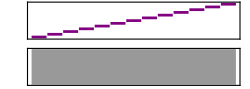

```mathematica
Sound[Table[SoundNote[i],{i,0,12}]]
```

构建 C 大调白键和弦表，按｛根音，三音，五音，七音，九音｝排序

```mathematica
Major={0,4,7,11,14}; (* 大九和弦 *)
Minor={0,3,7,10,14}; (* 小九和弦 *)
Clist={
(* C *) Major,
(* Dm *) Minor+2,
(* Em *) Minor+4,
(* F *) Major+5,
(* G *) Major+7,
(* Am *) Minor+9,
(* Bdim *) {0,3,6,10,13}+11
};
(* 扩充一遍升八度的 *)
Clist=Join[Clist,Clist+12];
```

按分解和弦的规则重排各列顺序｛根音，五音，七音，^根音，九音，^三音，^五音，^七音，^^根音…｝

```mathematica
Colist=Table[{Clist⟦i,1⟧,Clist⟦i,3⟧,Clist⟦i,4⟧,Clist⟦i,1⟧+12,Clist⟦i,5⟧,Clist⟦i,2⟧+12},{i,1,7*2}];
(* 扩充两遍升八度的 *)
Colist=ArrayFlatten[{{Colist,Colist⟦All,2;;6⟧+12,Colist⟦All,2;;6⟧+24}}];
```

错误范例：六部同向的分解和弦

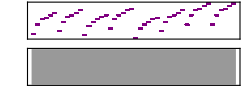

```mathematica
Sound[Table[SoundNote[Colist⟦i,j⟧,.2],
{i,{4,5,3,6,2,5,1+7,1+7}},(* 华语第二用烂的和弦进行 *)
{j,1,6}]]
```

搜索四声部解决方向不全同、最平稳进行的方案
暂时不考虑变底音的情况（最下层总是根音和五音）
为了允许串声部，设 p、f 记录了前后声部音符组合（元素个数相等），scor 首先找完全相同的音，每个 +10 分，剩下的后音找距离最近的前音，距离奇数个半音 -10 分，偶数个 -1 分

```mathematica
ifoddx10[n_]:=If[OddQ[n],10n,n]
scor[p_,f_]:=Module[{l=Select[f,!MemberQ[p,#]&]},
10(Length[f]-Length[l])-Total[Abs[Table[ifoddx10[l⟦i⟧-Nearest[p,l⟦i⟧]⟦1⟧],{i,1,Length[l]}]]]
]
```

例

```mathematica
scor[{1,2,3},{1,3,4}]
```

10

```mathematica
scor[{1,2,3},{1,3,5}]
```

18

输入：pre：前一个和弦已选好的右手 list（自动识别声部个数 n≥1）
fol：后一个和弦的右手的备选 list（m>n）
（两个 list 按从低到高排好序）
（算法暂时就 C_m^n 全试一遍好了反正元素个数又不多…）

```mathematica
Solv[pre_,fol_]:=Module[{
(* 列出所有子集 *)
s=Subsets[fol,{Length[pre]}]},
(* 计算各声部平稳度并取分数最高者 *)
Return[s⟦Ordering[Table[scor[pre,s⟦i⟧],{i,1,Length[s]}],-1]⟧];
]
```

用法举例：从 F 到 G 和弦，F 的右手取 3~5 列，求 G 和弦的平稳进行音

```mathematica
Colist⟦4,3;;5⟧
```

{16,17,19}

```mathematica
Solv[Colist⟦4,3;;5⟧,Colist⟦5⟧]⟦1⟧
```

{18,19,21}

用函数迭代决策出整个和弦进行的右手音
cp：输入简谱的和弦进行（其实是和弦表的行号）
first：输入第一个和弦的右手选择哪几列（≥3，因为最下面俩总是根音和五音）

```mathematica
ChordPro[cp_,first_]:=Module[
{ini=Table[Colist⟦i,3;;16⟧,{i,cp}]}, (* 此处 j 从 3 开始排除了最下面俩音（左手弹的） *)
ini⟦1⟧=ini⟦1,first⟧;
Table[ini⟦n+1⟧=Solv[ini⟦n⟧,ini⟦n+1⟧]⟦1⟧,
{n,1,Length[cp]-1}];
Return[ArrayFlatten[{{Table[Colist⟦i,1;;2⟧,{i,cp}],ini}}] ] (* 此处补回左手音） *)
]
```

使用范例

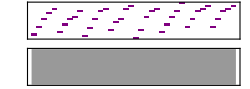

```mathematica
cl=ChordPro[{4,5,3,6,2,5,1+7,1+7} ,{3,5,6,7}]; 
Sound[Table[SoundNote[cl⟦i,j⟧,.2],{i,1,8},{j,1,5}]]
```

### 节奏型库

此模块将数组翻译成 SMSP 语言的织体谱子，需要用到 yxlllc 所开发的编译器

```mathematica
Music[s_]:=MusicCreate@SMSPCompile[StringJoin["m[4,120,0]
<chords.txt\n z[1,3>\n",s],"CChordExtend"->True,"Directory"->"E:/"]
```

最常用的：左手柱式，右手四分音符柱式，末尾加花

```mathematica
PianoL[cp_]:=Module[{l=ChordPro[cp,{3,4,5}]},
StringJoin[Table[{
StringReplace[ToString[l⟦i,1;;2⟧],{" "->"","{"->"[","}"->"> "}],
"s-_ 0= b= 0= b= | "
},{i,1,Length[cp]}]]
]
```

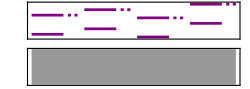

```mathematica
Music["[t1] i[Midi[Piano]] v[1]
[t1] |0] "<>PianoL[{4,5,3,6}]]
```

```mathematica
PianoR[cp_]:=Module[{l=ChordPro[cp,{3,4,5}]},
StringJoin[Table[{
StringReplace[ToString[l⟦i,3;;5⟧],{" "->"","{"->"[","}"->"> "}],
"s s s z=+ 0= a_ | "
},{i,1,Length[cp]}]]
]
```

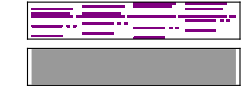

```mathematica
Music["[left] i[Midi[Piano,-24]] v[1]
[righ] i[Midi[Piano,-24]] v[.8]
[left] |0] "<>PianoL[{4,5,3,6}]<>"\n"<>
"[righ] |0] "<>PianoR[{4,5,3,6}]]
```

将左右手钢琴封装成织体模块，接收参数为和弦进行、初始列、左右手节奏型

```mathematica
PianoLR[cp_,start_,lepat_,ripat_]:=Module[{l=ChordPro[cp,start],left,righ},
left=StringJoin[Table[{
StringReplace[ToString[l⟦i,1;;2⟧],{" "->"","{"->"[","}"->"> "}],
lepat},{i,1,Length[cp]}]];
righ=StringJoin[Table[{
StringReplace[ToString[l⟦i,3;;(2+Length[start])⟧],{" "->"","{"->"[","}"->"> "}],
ripat},{i,1,Length[cp]}]];
Return["[left] i[Midi[Piano,-24]] v[1]
[righ] i[Midi[Piano,-24]] v[.8]
[left] |0] "<>left<>"\n"<>
"[righ] |0] "<>righ]
]
```

```mathematica
Music[PianoLR[{4,5,3,6},{3,4,5},"s-_ 0= b= 0= b= | ","s s s z=+ 0= a_ | "]]
```

-Graphics-

封装之后，换个节奏型就很方便了（参考哔站编曲教程 av9719573 钢琴高级技巧部分）

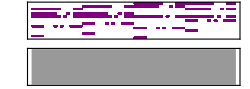

```mathematica
Music[PianoLR[{4,5,3,6},{3,4,5},"s 0_= b= 0= b= 0_ b | ","s s z=+ 0= a= b= 0= s_= | "]]
```

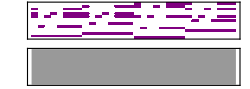

```mathematica
Music[PianoLR[{4,5,3,6},{3,4,5},"a_` b_ 0 b- &| ","s_ 0_ a_ b_ 0_ s_- | "]]
```

快节奏的

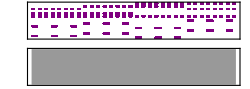

```mathematica
Music[PianoLR[{4,5,3,6},{3,4,5},"s_ 0 s_ 0 s_| ","s= 0= s= 0= s= 0= s= 0= s= 0= s= 0= s= 0= s= 0= | "]]
```

轻快地

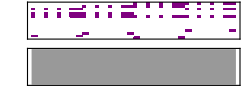

```mathematica
Music[PianoLR[{4,5,3,6},{3,4,5},"a_ 0_--_ a_| ","s= 0_= s= 0_= s= 0_= s | "]]
```

抒情地

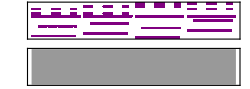

```mathematica
Music[PianoLR[{4,5,3,6},{3,4,5},"a_` b=_ b=_ b=_ b_ b= &| ","s=_ a=_ s=_ a=_ s_ a= | "]]
```